## Definitions

#### Power structure examples

```mathematica
SetParameters[<|"β"->2,"μ"->3,"λ"->1,"ρ"->0.9,"δ"->0.9,"α"->2.25, "k"->9|>];f[ps_]:=ShowPowerStructure[ps,<|"circular"->True,"size"->{100,100}|>];
SpacedRow[Map[Framed,{
f[PowerStructure[{2,.5,.8,1.5,.5,1}/2,({{0, 1, 1, 1, -1, 1}, {1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0}})]],
f[PowerStructure[{2,.5,.5,2,1,.5}/2,({{0, -1, -1, 0, 0, 1}, {-1, 0, 0, 0, 0, 0}, {-1, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 0, 0}})]],
f[PowerStructure[{2,.5,.5,2,1,.5,.7,1.2}/2,({{0, 1, 1, 0, 0, 0, 0, 1}, {1, 0, 0, 0, 0, 0, 0, 0}, {1, 0, 0, 0, 0, 0, 0, 1}, {0, 0, 0, 0, 1, 1, 1, 0}, {0, 0, 0, 1, 0, 1, 0, 0}, {0, 0, 0, 1, 1, 0, 0, 0}, {0, 0, 0, 1, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0, 0, 0}})]]
}],25]
```

-Graphics--Graphics--Graphics-

#### Persian empire

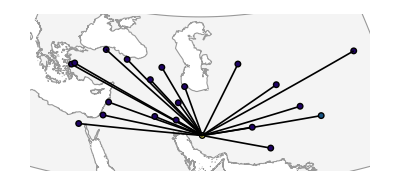
```mathematica
Framed[-Graphics-]
```

-Graphics-

## Axioms

## Data Structures

#### Cross-polytope 2D

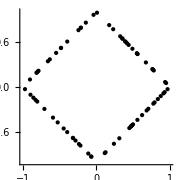

```mathematica
Show[{Graphics[Table[Point[RandomTactic[2]],75] , PlotRange->{{-1,1},{-1,1},{-1,1}}]},ImageSize->Small,Axes->True]
```

#### Cross-polytope 3D

```mathematica
Rasterize[Show[{
Graphics3D[{Scale[PolyhedronData["Octahedron","Faces"],1.4,{0,0,0}],Table[Point[RandomTactic[3]],1000]},Boxed->False,Method->{"ShrinkWrap"->True}]
}],ImageSize->Small,ImageResolution->5000]
```

-Graphics-

#### Cross-polytope social inertia

```mathematica
Rasterize[Show[{
Graphics3D[{
Scale[PolyhedronData["Octahedron","Faces"],1.4,{0,0,0}],
Style[Point[{.6,-.2,.2}],Red,PointSize[0.02]],
Table[Point[RandomTacticNear[{.6,-.2,.2},1,.3]],250]
},Boxed->False,Method->{"ShrinkWrap"->True}]
}],ImageSize->Small,ImageResolution->5000]
```

-Graphics-

#### Continuous power structure - pretty data

<|s→(1.
0.939
0.93
0.007),T→(0.927 | 0. | -0.029 | 0.028
0.034 | 0.935 | -0.013 | 0.019
0.022 | -0.033 | 0.943 | -0.03
0.017 | 0.032 | 0.015 | 0.923)|>

#### Continuous power structure - diagram

```mathematica
ps=<|"s"->({{1.}, {0.9390000000000001}, {0.93}, {0.007}}),"T"->({{0.927, 0., -0.029, 0.028}, {0.034, 0.935, -0.013000000000000001, 0.019}, {0.022, -0.033, 0.9430000000000001, -0.03}, {0.017, 0.032, 0.015, 0.923}})|>;
ShowPowerStructure[ps,<|"labels"->True,"ternary"->False,"circular"->True,"size"->{250,250}|>]
```

-Graphics-

#### Continuous power structure - pretty T

```mathematica
Pretty[ToTernary[({{0.927, 0., -0.029, 0.028}, {0.034, 0.935, -0.013000000000000001, 0.019}, {0.022, -0.033, 0.9430000000000001, -0.03}, {0.017, 0.032, 0.015, 0.923}})]]
```

(0 | 0 | -1 | 1
1 | 0 | -1 | 1
1 | -1 | 0 | -1
1 | 1 | 1 | 0)

#### Continuous power structure - symmetric T

```mathematica
Pretty[SymmetrizeT[ToTernary[({{0.927, 0., -0.029, 0.028}, {0.034, 0.935, -0.013000000000000001, 0.019}, {0.022, -0.033, 0.9430000000000001, -0.03}, {0.017, 0.032, 0.015, 0.923}})]]]
```

(0 | 0 | -1 | 1
0 | 0 | -1 | 1
-1 | -1 | 0 | -1
1 | 1 | -1 | 0)

#### Continuous power structure - symmetrized pretty

```mathematica
Pretty[PowerStructure[ps["s"],SymmetrizeT[ToTernary[ps["T"]]]]]
```

<|s→(1.
0.939
0.93
0.007),T→(0.9 | 0. | -0.033 | 0.033
0. | 0.9 | -0.033 | 0.033
-0.05 | -0.05 | 0.9 | -0.033
0.05 | 0.05 | -0.033 | 0.9)|>

#### Continuous power structure - symmetrized diagram

```mathematica
ShowPowerStructure[ps,<|"ternary"->True,"circular"->True,"size"->{100,100}|>]
```

-Graphics-

#### SymmetricTsNear example

```mathematica
SpacedRow[Map[Pretty,SymmetricTsNear[ZeroMatrix[3],1]],10]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)(0.9 | -0.1 | 0.
-0.1 | 0.9 | 0.
0. | 0. | 1.)(0.9 | 0.1 | 0.
0.1 | 0.9 | 0.
0. | 0. | 1.)(0.9 | 0. | -0.1
0. | 1. | 0.
-0.1 | 0. | 0.9)(0.9 | 0. | 0.1
0. | 1. | 0.
0.1 | 0. | 0.9)

#### Gravitized tactics

```mathematica
SetParameters[<|"β"->2.,"μ"->5.,"λ"->0.995,"α"->2.25,"δ"->0.8,"ρ"->0.8,"k"->9|>];s={.8,1,.2,.3,.6,.3};ShowPowerStructure[PowerStructure[s,GravitizeTernaryT[({{0, 0, 0, 0, 0, 0}, {1, 1, 0, 0, 0, 0}, {1, 0, 1, 0, 0, 0}, {-1, 0, 0, 1, 0, 0}, {1, 0, 0, 0, 1, 0}, {1, 0, 0, 0, 0, 1}}),s]],<|"ternary"->False,"size"->{175,175},"circular"->True|>]
```

-Graphics-

## Parameters